## Point and Space Groups

## Introduction

Demos of point and space groups

A point group is a group of rotations and reflections around some point. A space group is a point group with offsets (shifts, translations) added. These offsets can be continuous or discrete, and in the latter case, they are  combinations of integer multiples of some unit offsets.

What kinds
(# space dimensions) + (# lattice dimensions):
-- (how many of them):
1+0 - 1D point groups
-- 2
1+1 - Line groups
-- 2
2+0 - 2D point groups: rosette groups
-- 2 infinite families
2+1 - 2D line groups: Frieze groups
-- 7
2+2 - Wallpaper groups
-- 17
3+0 - 3D point groups: axial and quasi-spherical groups
-- Axial: 7 infinite families, quasi-spherical: 7
3+1 - 3D line groups: cylinder groups
-- 13 infinite families

Main functions:  ShowGroup[] and DisplayAll[]
The first argument in both functions is {# space dimensions, # lattice dimensions}.

ShowGroup[]
type: group type with optional space + extension for display variant
number(s) of repeats, linear and/or circular
display type

The display type: “Flags” or “Colors”
If “Flags”, then that is the last argument
If “Colors”, then further arguments:
(for 3D): ntess (tessellation (subdivision) factor)
colors (may be more than one arg)

DisplayAll[]
number(s) of repeats, linear and/or circular
(for 3D): ntess (tessellation number)
colors (may be more than one arg), like for ShowGroup[]

```mathematica
NotebookEvaluate[NotebookDirectory[] <> "Rotation Reflection - Matrices Groups Polytopes.nb"]
```

### Lists of Groups

Line groups (1D) - rosette groups (2D point ones)
Parameters: n = number of repeats around the origin
(Line group) - (1D point group) - (Rosette group)
p - C - C(n)
pm -  D - D(n)
Line groups: Hermann-Mauguin
Point groups: Schoenflies-like

ShowGroup[{1,1}, type, repeats, “Flags”]
repeats: number of linear repeats
ShowGroup[{1,1}, type, repeats, “Colors”, colors]
colors: for the ends of the line
DisplayAll[{1,1}, repeats, thick, colors]
thick: line thickness

ShowGroup[{2,0}, type, n, “Flags”]
n: number of repeats in a circle
ShowGroup[{2,0}, type, n, “Colors”, ntess, colors]
colors are are for {center, edge 1, edge 2} where the last two are repeated on the edge
DisplayAll[{2,0}, n, ntess, colors]

Frieze groups (2D line ones) - axial groups (3d point ones)
Parameters: n = number of repeats around the axis
(Frieze group) - (2D point group) - (Symbol): (Axial group) - (variants in the demos)
p1 - C1 - C: C(n)
p11m - D1 h - Ch:  C(n,h)
p11g - D1 h - Cs: S(2n)  - h, v
p1m1 - D1 v  - Cv:: C(n,v)
p2 - C2 - D: D(n)  - h, v
p2mm - D2 - Dh: D(n,h)
p2mg - D2 - Dd: D(n,d) - h, v
Frieze groups: Hermann-Mauguin
Point groups: Schoenflies and Schoenflies-like

ShowGroup[{2,1}, type, repeats, “Flags”]
repeats: number of linear repeats
ShowGroup[{2,1}, type, repeats, “Colors”, colors]
colors: for each rectangle
DisplayAll[{2,1}, repeats, colors]

ShowGroup[{3,0}, type, n, “Flags”]
n: number of repeats in a circle
ShowGroup[{3,0}, type, n, “Colors”, ntess, colorsfull, colorssemi]
colorsfull: colors for a complete lune: {N pole, equator 1, equator 2, S pole}
colorssemi: colors for a semilune: {pole, equator 1, equator 2}
DisplayAll[{3,0}, n, ntess, colorsfull, colorssemi]

Wallpaper groups (2D plane ones) - cylinder groups (3D line ones)
(Wallpaper group) - (My cylinder-group symbol) - (variants in the demos)
p1 - C
p2 - D - variants: h, v
pm:
p11m - Ch
p1m1 - Cv
pg:
p11g - Cs
p1g1 - Cvx
cm:
c11m - Chz
c1m1 - Cvz
pmm
p2mm - Dh
pmg:
p2mg - Dd
p2gm - Dhx
pgg:
p2gg - Ddx - variants: h, v
cmm:
c2mm - Dhz - variants: h, v
p4 - variants: a, d
p4m
p4g
p3 - variants: variants: p, e
p3m1
p31m
p6 - variants: p, e
p6m
Wallpaper groups: Hermann-Mauguin
Point groups: Schoenflies and Schoenflies-like
My cylinder-group symbols have these extensions of my Schoenflies-like symbols:
- x: axial offset 1/2 for v reflections
- z: zigzag along axis: 0, 1/2, much like Cs axial reflections

ShowGroup[{2,2}, type, rpts1, rpts2, “Flags”]
rpts1: number of horizontal linear repeats
rpts2: number of vertical linear repeats
ShowGroup[{2,2}, type, rpts1, rpts2, “Colors”, colorsrect, colorstri]
colorsrect: colors of rectangles
colorstri: colors of triangles
DisplayAll[{2,2}, rpts1, rpts2, colorsrect, colorstri]

ShowGroup[{3,1}, type, n, axrpts, “Flags”]
n: number of repeats in a circle
axrpts: number of repeats along the axis
ShowGroup[{3,1}, type, n, axrpts, “Colors”, ntess, colors]
colors: colors of bent rectangles
DisplayAll[{3,1}, n, axrpts, ntess, colors]

Quasi-spherical point groups
The demos are for groups V, Vh, T, Th, Td, O, Oh, I, and Ih.
V - the Viergruppe (4-group) or dihedral group D2
Vh - V with inversions: D2h
T - the tetrahedral group, for the regular tetrahedron
Th - T with inversions
Td - T with mirror-image symmetries of the tetrahedron
O - the octahedral group, for the cube and the regular octahedron
Oh - O with inversions
I - the icosahedral group, for the regular dodecahedron and icosahedron
Ih - I with inversions

The display function shows triangles formed from adjacent vertices, edges, and faces. These are colored according to their parities, if the group keeps parities distinct.

For Vh, Td, Oh, and Ih, the triangles have no parities.
For V, T, Th, O, and I, the triangles do have parities, and these parities are assigned different colors.

For V, T, O, and I, the triangles have parity det({v,e,f}), because that is unchanged by the group.

The remaining one, Th, is a special case. It uses octahedral triangles, because Th’s reflections do (vertex) <-> (face), and these are both octahedral-face locations. So the triangles have parity det({v,e,f})*parity(f), because that is unchanged by this group. Octahedral faces have opposite parities from their neighbors, one parity being tetrahedron vertices, and the other parity being tetrahedron faces.

ShowGroup[{3,0}, type, “Flags”]
ShowGroup[{3,0}, type, “Colors”, ntess, colorsets]
colorsets: three sets of {vertex color, edge color, face color} for the corresponding triangle-faced polyhedron
The three sets are for both parities, for positive parity, and for negative parity, where the parity is for each side
DisplayAll[{3,0}, ntess, colors]

## Shared Functions

```mathematica
RepeatHoriz[g_,n_] := Table[Translate[g,{k,0}],{k,0,n-1}]
```

```mathematica
RepeatRect[g_,n1_,n2_] := Table[Translate[g,{k1,k2}],{k1,0,n1-1},{k2,0,n2-1}]
```

```mathematica
RepeatVert[g_,n_,step_:1] := Table[Translate[g,{0,0,step*k}],{k,0,n-1}]
```

```mathematica
HexPoints[n1_,n2_] := Table[{{1,1/2},{0,Sqrt[3]/2}}.{k1,k2},{k1,0,n1-1},{k2,0,n2-1}]
```

```mathematica
RepeatTri[g_,n1_,n2_] := Table[Translate[g,{{1,1/2},{0,Sqrt[3]/2}}.{k1,k2}],{k1,0,n1-1},{k2,0,n2-1}]
```

```mathematica
(* For all rectangular groups: all frieze groups and all but the triangular and hexagonal wallpaper groups*)
```

```mathematica
RectTfm[m11_,m22_,d1_,d2_] := {{{m11,0},{0,m22}},{d1,d2}}
```

```mathematica
MakeScaleMatrix[scale_] := Which[Length[scale]==0,scale*id2,Length[Dimensions[scale]]==1,DiagonalMatrix[scale],True,scale]
```

```mathematica
PlnGrpTfm[grpargs_,scale_,offsets_] := Module[{mats,nrpt,xpofsts},
mats = If[Length[grpargs] > 3,Flatten[ConstantArray[Group2D @@ Take[grpargs,3],grpargs[[4]]],1], Group2D @@ grpargs];
nrpt = Length[mats]/Length[offsets];
xpofsts = Flatten[ConstantArray[#,nrpt]& /@ offsets,1];
Table[{mats[[k]].MakeScaleMatrix[scale],mats[[k]].xpofsts[[k]]},{k,Length[mats]}]
]
```

```mathematica
PlnGrpTfm[grpargs_,scale_] := PlnGrpTfm[grpargs,scale,{{0,0}}]
```

```mathematica
PlnGrpTfm[grpargs_] := PlnGrpTfm[grpargs,1]
```

```mathematica
SelectTfm[tfm_] := If[Head[tfm[[1,1]]] === String,PlnGrpTfm @@ tfm, RectTfm @@@ tfm]
```

```mathematica
(* In bounding boxes -1/2 to 1/2 in both dimensions*)
```

```mathematica
FlagShape[] := Module[{PoleBottom = -0.3, PoleTop = 0.3, FlagTipPoleExtent = 0.1,FlagTipOnPole,FlagStartOnPole,PoleWidth = 0.05,PoleBack, PoleFront, FlagOutwardExtent = 0.3,FlagFront},
FlagTipOnPole = PoleTop - FlagTipPoleExtent; FlagStartOnPole = PoleTop - 2*FlagTipPoleExtent;
PoleBack =-PoleWidth/2;
PoleFront = PoleWidth/2;
FlagFront = PoleFront + FlagOutwardExtent;
Polygon[{{PoleBack,PoleBottom},{PoleBack,PoleTop},{PoleFront,PoleTop},{FlagFront,FlagTipOnPole},{PoleFront,FlagStartOnPole},{PoleFront,PoleBottom}}]
]
```

```mathematica
RectShape[colors_List] :=Polygon[(1/2){{-1,-1},{1,-1},{1,1},{-1,1}},VertexColors->colors]
```

```mathematica
TriShape[colors_List] := Polygon[{{0,0},{1,0},{0,1}},VertexColors->colors]
```

```mathematica
FlagShape3D[] := Module[{PoleBottom = -0.3, PoleTop = 0.3, FlagTipPoleExtent = 0.1,FlagTipOnPole,FlagStartOnPole,PoleWidth = 0.05,PoleBack, PoleFront, FlagOutwardExtent = 0.3,FlagFront,pole,flag},
FlagTipOnPole = PoleTop - FlagTipPoleExtent; FlagStartOnPole = PoleTop - 2*FlagTipPoleExtent;
PoleBack =-PoleWidth/2;
PoleFront = PoleWidth/2;
FlagFront = PoleFront + FlagOutwardExtent;
pole = Cylinder[{{0,0,PoleBottom},{0,0,PoleTop}},PoleWidth/2];
flag = Polygon[{{PoleFront,0,PoleTop},{FlagFront,0,FlagTipOnPole},{PoleFront,0,FlagStartOnPole}}];
{pole,flag}
]
```

```mathematica
FlagShape3D[1] := Module[{PoleBottom = -0.3, PoleTop = 0.3, FlagTipPoleExtent = 0.1,FlagTipOnPole,FlagStartOnPole,PoleWidth = 0.05,PoleBack, PoleFront, FlagOutwardExtent = 0.3,FlagFront,pole,flag},
FlagTipOnPole = PoleTop - FlagTipPoleExtent; FlagStartOnPole = PoleTop - 2*FlagTipPoleExtent;
PoleBack =-PoleWidth/2;
PoleFront = PoleWidth/2;
FlagFront = PoleFront + FlagOutwardExtent;
pole = Cylinder[{{0,0,PoleBottom},{0,0,PoleTop}},PoleWidth/2];
flag = Polygon[{{PoleFront,0,PoleTop},{FlagFront,0,FlagTipOnPole},{PoleFront,0,FlagStartOnPole}}];
{pole,flag}
]
```

```mathematica
FlagShape3D[2] := Module[{PoleBottom = -0.3, PoleTop = 0.3, FlagTipPoleExtent = 0.1,FlagTipOnPole,FlagStartOnPole,PoleWidth = 0.05,PoleBack, PoleFront, FlagOutwardExtent = 0.3,FlagFront,pole,flag},
FlagTipOnPole = PoleTop - FlagTipPoleExtent; FlagStartOnPole = PoleTop - 2*FlagTipPoleExtent;
PoleBack =-PoleWidth/2;
PoleFront = PoleWidth/2;
FlagFront = PoleFront + FlagOutwardExtent;
pole = Cuboid[{-PoleWidth/2,-PoleWidth/2,PoleBottom},{PoleWidth/2,PoleWidth/2,PoleTop}];
flag = Polygon[{{PoleFront,0,PoleTop},{FlagFront,0,FlagTipOnPole},{PoleFront,0,FlagStartOnPole}}];
{pole,flag}
]
```

```mathematica
FlagShape3D[] := FlagShape3D[2];
```

```mathematica
GetGroupType[type_] := First[StringSplit[type," "]]
```

## 1+1: Line groups

```mathematica
(* 1D to 2D for 2D graphics *)
```

```mathematica
ExpandGroup1DElement[m_] := DiagonalMatrix[{m[[1,1]],1}]
```

```mathematica
ExpandGroup1D[type_] := ExpandGroup1DElement /@ Group1D[type]
```

```mathematica
ShowGroup[{1,1},type_,repeats_?IsPosInt,"Flags"] := Module[{Tfm,grptype,numseg,arrowhead,UnitShape,grp,UnitCell},
Tfm = Switch[type,"p",{"C",1},
"pm",{"D",2},_,Null];
If[Tfm === Null,Return[]];
{grptype,numseg} = Tfm;
arrowhead = Polygon[{{1/6,0},{-1/6,1/12},{-1/12,0},{-1/6,-1/12}}];
UnitShape = Translate[arrowhead,{1/(2*numseg),0}];
grp = ExpandGroup1D[grptype];
UnitCell = GeometricTransformation[UnitShape,grp];
RepeatHoriz[UnitCell,repeats]
]
```

```mathematica
ShowGroup[{1,1},type_,repeats_?IsPosInt,"Colors",colors_List] := Module[{Tfm,grptype,grp,numseg,UnitShape,UnitCell},
Tfm = Switch[type,"p",{"C",1},
"pm",{"D",2},_,Null];
If[Tfm === Null,Return[]];
{grptype,numseg} = Tfm;
UnitShape = Line[{{0,0},{1/numseg,0}},VertexColors->colors];
grp = ExpandGroup1D[grptype];
UnitCell = GeometricTransformation[UnitShape,grp];
RepeatHoriz[UnitCell,repeats]
]
```

```mathematica
DisplayAll[{1,1},repeats_?IsPosInt,thick_,colors_List] := Table[{type,Graphics[ShowGroup[{1,1},type,repeats,"Flags"]],Graphics[{AbsoluteThickness[thick],ShowGroup[{1,1},type,repeats,"Colors",colors]}]},{type,{"p","pm"}}]
```

## 2+0: Rosette groups

```mathematica
ShowGroup[{2,0},type_,n_?IsPosInt,"Flags"] := Module[{Tfm,numseg,flag,scale,angofst,flagscof,flagflip,UnitShape,UnitCell},
Tfm = Switch[type,"C",1,"D",2,_,Null];
If[Tfm == Null,Return[]];
numseg = Tfm;
flag = FlagShape[];
scale = Min[1,12/(numseg*n)];
angofst = N[Pi/n]/Switch[numseg,1,1,2,Min[Max[2,n/2],3]];
flagscof = GeometricTransformation[flag,{scale*id2,{0,1}}];
flagflip = GeometricTransformation[flagscof, Matrix2DTrig[-1,Pi/2]];
UnitCell = GeometricTransformation[flagflip,Matrix2DTrig[1,angofst]];
{GeometricTransformation[UnitCell,Group2D[type,n]],{Thick,Circle[{0,0},1+(1/2)scale]}}
]
```

```mathematica
PieSlice[n_?IsPosInt,ndiv_?IsPosInt,colors_List] := Module[{ptfracs,edpts,pts,edclrs,clrs,trivts},
(* Fractions along the perimeter from the first point to the second one. *)
ptfracs = Range[0,ndiv]/N[ndiv];
(* Perimeter points *)
edpts = CosSin[(2Pi)/n*ptfracs];
 (* Add the center point *)
pts = Prepend[edpts,{0,0}];
(* Perimeter colors *)
edclrs =(f |-> Blend[Rest[colors],f]) /@ ptfracs;
(* Add the center color *)
clrs = Prepend[edclrs,First[colors]];
(* Subslice triangles by vertex index *)
trivts = Table[{1,k+2,k+3},{k,0,ndiv-1}];
(* Assemble these pieces *)
GraphicsComplex[pts,Polygon[trivts],VertexColors->clrs]
]
```

```mathematica
ShowGroup[{2,0},type_,n_?IsPosInt,"Colors",ntess_?IsPosInt,colors_List] := Module[{Tfm,nslice,ndiv,UnitShape},
Tfm = Switch[type,"C",1,"D",2,_,Null];
If[Tfm === Null,Return[]];
nslice = n*Tfm;
ndiv = Ceiling[(2Pi)*ntess/n];
UnitShape = PieSlice[nslice,ndiv,colors];
GeometricTransformation[UnitShape,Group2D[type,n]]
]
```

```mathematica
DisplayAll[{2,0},n_?IsPosInt,ntess_?IsPosInt,colors_List] := Table[{type,Graphics[ShowGroup[{2,0},type,n,"Flags"]],Graphics[ShowGroup[{2,0},type,n,"Colors",ntess,colors]]},{type,{"C","D"}}]
```

## 2+1: Frieze groups

```mathematica
ShowGroup[{2,1},type_,repeats_?IsPosInt,"Flags"] := Module[{Tfm,scl,ofst,UnitShape,grptype,UnitCell},
Tfm = Switch[type,"p1",{1,{0,0}},"p11m",{1,{0,1/2}},"p11g",{1,{0,0}},"p1m1",{1,{1/8,0}},"p2 h",{1,{0,1/2}},"p2 v",{1,{1/4,0}},"p2mm",{1,{1/8,1/2}},"p2mg",{1,{-1/8,1/2}},_,Null];
If[Tfm===Null,Return[]];
{scl,ofst} = Tfm;
UnitShape = Translate[Scale[FlagShape[],scl],ofst];
grptype = GetGroupType[type];
UnitCell = GeometricTransformation[UnitShape,Group2D1L[grptype]];
RepeatHoriz[UnitCell,repeats]
]
```

```mathematica
ShowGroup[{2,1},type_,repeats_?IsPosInt,"Colors",colors_List] := Module[{Tfm,scl,ofst,UnitShape,grptype,UnitCell},
Tfm = Switch[type,"p1",{1,{0,0}},"p11m",{{1,1/2},{0,1/4}},"p11g",{{1/2,1},{0,0}},"p1m1",{{1/2,1},{1/4,0}},"p2 h",{{1,1/2},{0,1/4}},"p2 v",{{1/2,1},{1/4,0}},"p2mm",{1/2,{1/4,1/4}},"p2mg",{1/2,{0,1/4}},_,Null];
If[Tfm===Null,Return[]];
{scl,ofst} = Tfm;
UnitShape = Translate[Scale[RectShape[colors],scl],ofst];
grptype = GetGroupType[type];
UnitCell = GeometricTransformation[UnitShape,Group2D1L[grptype]];
RepeatHoriz[UnitCell,repeats]
]
```

```mathematica
DisplayAll[{2,1},repeats_?IsPosInt,colors_List] := Table[{type,Graphics[ShowGroup[{2,1},type,repeats,"Flags"]],Graphics[ShowGroup[{2,1},type,repeats,"Colors",colors]]},{type,{"p1","p11m","p11g","p1m1","p2 h","p2 v","p2mm","p2mg"}}]
```

## 2+2: Wallpaper groups

```mathematica
AddFixesToTfms[tfms_,fixes_] := Module[{n},
If[fixes =!= Null,
n = Length[tfms];
Table[{tfms[[i,1]],tfms[[i,2]]+fixes[[i]]},{i,n}],
tfms
]
]
```

```mathematica
ShowGroup[{2,2},type_,rpts1_?IsPosInt,rpts2_?IsPosInt,"Flags"] := Module[{Tfm,GridType,scl,ofst,flag,UnitShape ,grptype,UCFixes,UnitCell,rptfunc},
Tfm = Switch[type,"p1",{"Obl",1,{0,0}},"p2 h",{"Obl",1/2,{0,1/4}},"p2 v",{"Obl",1,{-1/3,0}},"p11m",{"Rect",1/2,{0,1/4}},"p1m1",{"Rect",1,{-3/8,0}},"p11g",{"Rect",1,{-1/4,0}},"p1g1",{"Rect",1/2,{0,1/4}},"c11m",{"Rect",1/2,{-1/4,1/4}},"c1m1",{"Rect",1/2,{-1/4,1/4}},"p2mm",{"Rect",1/2,{-1/3,1/4}},"p2mg",{"Rect",1/2,{-1/6,1/4}},"p2gm",{"Rect",1/2,{-1/4,0}},"p2gg h",{"Rect",1/4,{0,1/8}},"p2gg v",{"Rect",1/2,{-1/6,0}},"c2mm h",{"Rect",1/4,{1/4,3/8}},"c2mm v",{"Rect",1/2,{1/8,1/4}},"p4 a",{"Sqr",1/2,{0,1/4}},"p4 d",{"Sqr",1/2,{1/4,1/4}},"p4m",{"Sqr",1/3,{1/6,1/3}},"p4g",{"Sqr",1/3,{1/8,1/8}},"p3 p",{"Tri",1/2,{0,1/4}},"p3 e",{"Tri",1/2*{{0,1},{-1,0}},{0,-1/4}},"p31m",{"Tri",1/3,{1/4,1/4/Sqrt[3]}},"p3m1",{"Tri",1/3,{1/3,0}},"p6 p",{"Tri",1/2,{0,1/4}},"p6 e",{"Tri",1/2,{1/3,0}},"p6m",{"Tri",1/4,{1/3,1/6/Sqrt[3]}},_,{Null,Null}];
If[Tfm === Null,Return[]];
UCFixes = Switch[type,"c11m",{{0,0},{0,1},{0,0},{0,0}},"c1m1",{{0,0},{0,0},{0,0},{-1,0}},"c2mm h",{{0,0},{0,1},{0,1},{0,0},{-1,0},{0,0},{-1,0},{0,0}},"c2mm v",{{0,0},{0,1},{0,1},{0,0},{-1,0},{0,0},{-1,0},{0,0}},"p4g",{{0,0},{1,0},{1,0},{0,0},{0,0},{0,-1},{0,-1},{0,0}},_,Null];
{GridType,scl,ofst} = Tfm;
scl = MakeScaleMatrix[scl];
flag = FlagShape[];
UnitShape = GeometricTransformation[flag,{scl,ofst}];
grptype = GetGroupType[type];
UnitCell=GeometricTransformation[UnitShape,AddFixesToTfms[Group2D2L[grptype],UCFixes]];
rptfunc = Switch[GridType,
"Obl"|"Rect"|"Sqr",RepeatRect,"Tri",RepeatTri];
rptfunc[UnitCell,rpts1,rpts2]
]
```

```mathematica
ShowGroup[{2,2},type_,rpts1_?IsPosInt,rpts2_?IsPosInt,"Colors",rectcolors_List,tricolors_List] := Module[{Tfm,GridType,ShapeType,scl,ofst,shape,UnitShape ,UnitCell,grptype,UCFixes,rptfunc},
Tfm = Switch[type,"p1",{"Obl","Rect",1,{0,0}},"p2 h",{"Obl","Rect",{1,1/2},{0,1/4}},"p2 v",{"Obl","Rect",{1/2,1},{-1/4,0}},"p11m",{"Rect","Rect",{1,1/2},{0,1/4}},"p1m1",{"Rect","Rect",{1/2,1},{-1/4,0}},"p11g",{"Rect","Rect",{1/2,1},{-1/4,0}},"p1g1",{"Rect","Rect",{1,1/2},{0,1/4}},"c11m",{"Rect","Rect",1/2,{-1/4,1/4}},"c1m1",{"Rect","Rect",1/2,{-1/4,1/4}},"p2mm",{"Rect","Rect",1/2,{-1/4,1/4}},"p2mg",{"Rect","Rect",1/2,{0,1/4}},"p2gm",{"Rect","Rect",1/2,{-1/4,0}},"p2gg h",{"Rect","Rect",{1,1/4},{0,1/8}},"p2gg v",{"Rect","Rect",{1/4,1},{-1/8,0}},"c2mm h",{"Rect","Rect",{1/2,1/4},{1/4,1/8}},"c2mm v",{"Rect","Rect",{1/4,1/2},{1/8,1/4}},"p4 a",{"Sqr","Tri",1/2{{-1,1},{1,1}},{0,0}},"p4 d",{"Sqr","Rect",1/2,{1/4,1/4}},"p4m",{"Sqr","Tri",1/2,{-1/2,0}},"p4g",{"Sqr","Tri",1/2,{0,0}},"p3 p",{"Tri","Rect",{1/2{1,1},Sqrt[3]/6{1,-1}},{0,Sqrt[3]/6}},"p3 e",{"Tri","Rect",{1/2{1,1},Sqrt[3]/6{1,-1}},{0,-Sqrt[3]/6}},"p31m",{"Tri","Tri",{1/2{-1,1},Sqrt[3]/6{-1,-1}},{1/2,Sqrt[3]/6}},"p3m1",{"Tri","Tri",{1/2{-1,-1},Sqrt[3]/6{1,-1}},{0,0}},"p6 p",{"Tri","Tri",{1/2{-1,-1},Sqrt[3]/6{1,-1}},{0,0}},"p6 e",{"Tri","Tri",{1/2{1,-1},Sqrt[3]/6{-1,-1}},{1/2,Sqrt[3]/6}},"p6m",{"Tri","Tri",{1/2,Sqrt[3]/6},{-1/2,0}},_,{Null,Null}];
If[Tfm === Null,Return[]];
UCFixes = Switch[type,"c11m",{{0,0},{0,1},{0,0},{0,0}},"c1m1",{{0,0},{0,0},{0,0},{-1,0}},"c2mm h",{{0,0},{1,0},{0,0},{1,0},{0,0},{0,0},{0,0},{0,0}},"c2mm v",{{0,0},{0,1},{0,1},{0,0},{0,0},{0,0},{0,0},{0,0}},"p4g",{{0,0},{0,0},{0,1},{0,1},{-1,0},{-1,0},{0,0},{0,0}},"p31m",{{-1,0},{0,0},{1/2,Sqrt[3]/2},{-1,0},{0,0},{1/2,Sqrt[3]/2}},"p6 e",{{-1,0},{0,0},{0,0},{0,0},{1/2,Sqrt[3]/2},{-1/2,Sqrt[3]/2}},_,Null];
{GridType,ShapeType,scl,ofst} = Tfm;
scl = MakeScaleMatrix[scl];
shape = Switch[ShapeType,"Rect",RectShape[rectcolors],"Tri",TriShape[tricolors]];
UnitShape = GeometricTransformation[shape,{scl,ofst}];
grptype = GetGroupType[type];
UnitCell=GeometricTransformation[UnitShape,AddFixesToTfms[Group2D2L[grptype],UCFixes]];
rptfunc = Switch[GridType,
"Obl"|"Rect"|"Sqr",RepeatRect,"Tri",RepeatTri];
rptfunc[UnitCell,rpts1,rpts2]
]
```

```mathematica
DisplayAll[{2,2},rpts1_?IsPosInt,rpts2_?IsPosInt,rectcolors_List,tricolors_List] := Table[{type,Graphics[ShowGroup[{2,2},type,rpts1,rpts2,"Flags"]],Graphics[ShowGroup[{2,2},type,rpts1,rpts2,"Colors",rectcolors,tricolors]]},{type,{"p1","p2 h","p2 v","p11m","p1m1","p11g","p1g1","c11m","c1m1","p2mm","p2mg","p2gm","p2gg h","p2gg v","c2mm h","c2mm v","p4 a","p4 d","p4m","p4g","p3 p","p3 e","p31m","p3m1","p6 p","p6 e","p6m"}}]
```

## 3+0: Axial groups

```mathematica
ShowGroup[{3,0},type_,n_?IsPosInt,"Flags"] := Module[{Tfm,scl,ofst,flgscl,ta,UnitShape,UnitCell,grptype},
Tfm = Switch[type,"C",{1,{0,1,0}},"Ch",{1,{0,1,1/2}},"Cs",{1,{0,1,0}},"Cv",{1,{1/8,1,0}},"D h",{1,{0,1,1/2}},"D v",{1,{1/8,1,0}},"Dh",{1,{1/8,1,1/2}},"Dd",{1,{1/8,1,1/2}},_,Null];
If[Tfm===Null,Return[]];
{scl,ofst} = Tfm;
flgscl = Min[1,6/n];
scl = flgscl*scl;
ta = Pi/(2n);
ofst = {flgscl,1,flgscl}*ofst;
UnitShape = FlagShape3D[];
UnitCell = Translate[Scale[UnitShape,scl],ofst];
grptype = GetGroupType[type];
GeometricTransformation[UnitCell,Group3D[grptype,n]]
]
```

```mathematica
(* Much of the code is copied off of the PieSlice[] code for rosette groups *)
```

```mathematica
SemiLune[n_?IsPosInt,ndiv_?IsPosInt,ntess_?IsPosInt,colors_List] := Module[{lngfracs,latfracs,lngpts,latpts,llpts,pts,llclrs,clrs,ix,llixs,plix,quadvts,trivts,polyvts},
(* Longitude and latitude fractions *)
lngfracs = Range[0,ndiv]/N[ndiv];
latfracs = Range[0,ntess-1]/N[ntess] ;
(* Longitude and latitude points *)
lngpts = CosSin[(2Pi/n)*lngfracs];
latpts = CosSin[(Pi/2)*latfracs];
llpts = Flatten[Table[{latp[[1]]*lngp[[1]],latp[[1]]*lngp[[2]],latp[[2]]},{latp,latpts},{lngp,lngpts}],1];
 (* Add the pole point *)
pts = Append[llpts,{0,0,1}];
(* Longitude and latitude colors *)
llclrs = Flatten[Table[Blend[Take[colors,3],{latf,(1-latf)*(1-lngf),(1-latf)*lngf}],{latf,latfracs},{lngf,lngfracs}],1];
(* Add the pole color *)
clrs = Append[llclrs,First[colors]];
(* Find the point indexes *)
ix = 1;
llixs = Table[ix++,{lat,0,ntess-1},{lng,0,ndiv}];
plix = ix;
(* Find the quads *)
quadvts = Flatten[Table[{llixs[[lat+1,lng+1]],llixs[[lat+1,lng+2]],llixs[[lat+2,lng+2]],llixs[[lat+2,lng+1]]},{lat,0,ntess-2},{lng,0,ndiv-1}],1];
(* Find the triangles *)
trivts = Table[{llixs[[ntess,lng+1]],llixs[[ntess,lng+2]],plix},{lng,0,ndiv-1}];
(* Assemble these pieces *)
polyvts = quadvts ~ Join ~ trivts ;
GraphicsComplex[pts,Polygon[polyvts],VertexColors->clrs,VertexNormals->pts]
]
```

```mathematica
FullLune[n_?IsPosInt,ndiv_?IsPosInt,ntess_?IsPosInt,colors_List] := Module[{sl,slx},
sl = SemiLune[n,ndiv,ntess,colors[[{1,2,3}]]];
slx = GeometricTransformation[SemiLune[n,ndiv,ntess,colors[[{4,2,3}]]],DiagonalMatrix[{1,1,-1}]];
{sl,slx}
]
```

```mathematica
(* Takes the type of the group and returns {multipler for number of segmnets n, extent: pole-to-equator 0, pole-to-pole 1} *)
```

```mathematica
ShowGroup[{3,0},type_,n_?IsPosInt,"Colors",ntess_?IsPosInt,clrsfull_List,clrssemi_List] := Module[{Tfm,lnnum,lntype,USNum,USFunc,ndiv,UnitShape,grptype,colors},
Tfm = Switch[type,"C",{1,1},"Ch",{1,0},"Cs",{2,1},"Cv",{2,1},"D h",{1,0},"D v",{2,1},"Dh",{2,0},"Dd",{2,0},_,Null];
If[Tfm === Null,Return[]];
{lnnum,lntype} = Tfm;
USNum = n*lnnum;
USFunc = Switch[lntype,0,SemiLune,1,FullLune];
colors = Switch[lntype,0,clrssemi,1,clrsfull];
ndiv = Ceiling[(2Pi)*ntess/USNum];
UnitShape = USFunc[USNum,ndiv,ntess,colors];
grptype = GetGroupType[type];
GeometricTransformation[UnitShape,Group3D[grptype,n]]
]
```

```mathematica
DisplayAll[{3,0},n_?IsPosInt,ntess_?IsPosInt,clrsfull_List,clrssemi_List] := Table[{type,Graphics3D[ShowGroup[{3,0},type,n,"Flags"],SphericalRegion->True],Graphics3D[{EdgeForm[],ShowGroup[{3,0},type,n,"Colors",ntess,clrsfull,clrssemi]},SphericalRegion->True]},{type,{"C","Ch","Cs","Cv","D h","D v","Dh","Dd"}}]
```

## 3+0: Quasi-Spherical groups

```mathematica
ShowGroup[{3,0},type_,"Flags"] := Module[{FlagTfm,Flag},
FlagTfm = Switch[type,"V",{1,{1,1,1}},"Vh",{1,{1,1,1}},"T",{1,{0,1,1/2}},"Th",{1,{1/4,1,1/2}},"Td",{1,{0,1,1/2}},"O",{1,{0,1,1/2}},"Oh",{1,{1/8,1,1/2}},"I",{1/2,{0,1,0}},"Ih",{1/3,{0,1,1/6}},_,Null];
If[FlagTfm===Null,Return[]];
Flag = Translate[Scale[FlagShape3D[],FlagTfm[[1]]],FlagTfm[[2]]];
GeometricTransformation[Flag,Group3D[type]]
]
```

```mathematica
DirsVEF["V"] := Transpose[{id3,-id3}]
```

```mathematica
DirsVEF["T"] := {AllSignsEven[3],ExpandWithSignsMulti[id3],AllSignsOdd[3]}
```

```mathematica
DirsVEF["O"] := {ExpandWithSignsMulti[id3],ExpandWithSignsMulti[Permutations[{1,1,0}]],AllSigns[3]}
```

```mathematica
DirsVEF["I"] := Module[{qts},qts = GroupQt["I"];
Table[Rest /@ Select[qts,q |-> First[q] == csa],{csa,{(Sqrt[5]+1)/4,0,1/2}}]
]
```

```mathematica
ClosestIndexes[veclist_List,refvec_List] := Module[{vecprods,maxvp},
vecprods = Expand[veclist.refvec];
maxvp = Max[vecprods];
Select[Range[Length[vecprods]],ix |-> vecprods[[ix]] == maxvp]
]
```

```mathematica
ClosestIndxList[veclist_List,refvcList_List] := Table[ClosestIndexes[veclist,rfvc],{rfvc,refvcList}]
```

```mathematica
TrisVEF[dvef_List] := Module[{venr,vfnr,efnr,vteds,vei},
venr = ClosestIndxList[dvef[[2]],dvef[[1]]];
vfnr =  ClosestIndxList[dvef[[3]],dvef[[1]]];
efnr =  ClosestIndxList[dvef[[3]],dvef[[2]]];
vteds = Flatten[Table[{i,j},{i,Length[venr]},{j,venr[[i]]}],1];
Flatten[Table[vei = Intersection[vfnr[[ve[[1]]]],efnr[[ve[[2]]]]]; Table[{ve[[1]],ve[[2]],k},{k,vei}],{ve,vteds}],1]
]
```

```mathematica
TriVtsVEF[type_] := Module[{vtslst,trilst,nmvts},
vtslst = DirsVEF[type];
trilst =  TrisVEF[vtslst];
nmvts = Map[Normalize[N[#]]&,vtslst,{2}];
Table[nmvts[[k,t[[k]]]],{t,trilst},{k,3}]
]
```

```mathematica
ShowTris[type_] := Polygon[TriVtsVEF[type]]
```

```mathematica
TriTess[vts_List,ntess_?IsPosInt,colors_List] := Module[{flip,ix,tvixs,wts,trivts,triclrs,ofst1,ofst2,tris1,tris2,tris},
(* Need to keep constant orientation of the triangles *)
flip = Expand[Det[vts]] < 0;
ix = 1;
tvixs = Table[ix++,{i,0,ntess},{j,0,ntess-i}];
wts =  Flatten[Table[{ntess-i-j,j,i},{i,0,ntess},{j,0,ntess-i}],1]/N[ntess];
trivts = Table[Normalize[w.vts],{w,wts}];
triclrs = Table[Blend[colors,w],{w,wts}];
{ofst1,ofst2} = If[flip,{1,0},{0,1}];
tris1 = Table[{tvixs[[i+1,j+ofst1+1]],tvixs[[i+1,j+ofst2+1]],tvixs[[i+2,j+1]]},{i,0,ntess-1},{j,0,ntess-i-1}];
tris2 = Table[{tvixs[[i+2,j+ofst2+1]],tvixs[[i+2,j+ofst1+1]],tvixs[[i+1,j+2]]},{i,0,ntess-2},{j,0,ntess-i-2}];
;
tris =  Flatten[tris1,1] ~Join~ Flatten[tris2,1];
GraphicsComplex[trivts,Polygon[tris],VertexColors->triclrs,VertexNormals->trivts]
]
```

The colors are three lists of {vertex color, edge color, face color} for a triangle-faced polyhedron. The lists are for both parities, positive parity, and negative parity.

Here, the octahedral-face parity is the product of each face’s direction-vector components. Other formulations of octahedral-face locations may require different formulations.

```mathematica
ShowGroup[{3,0},type_,"Colors",ntess_?IsPosInt,colorsets_List] := Module[{TriType,Refl,bothclrs,posclrs,negclrs,clrs},
{TriType,Refl} = Switch[type,"V",{"V",0},"Vh",{"V",1},"T",{"T",0},"Th",{"O",2},"Td",{"T",1},"O",{"O",0},"Oh",{"O",1},"I",{"I",0},"Ih",{"I",1},_,{Null,Null}];
If[TriType===Null,Return[]];
{bothclrs,posclrs,negclrs} = colorsets;
Table[
clrs = Switch[Refl,0,If[Det[t]>0,posclrs,negclrs],1,bothclrs,2,If[(Det[t]*(Times @@ t[[3]]))>0,posclrs,negclrs]];
TriTess[t,ntess,clrs],
{t,TriVtsVEF[TriType]}]
]
```

```mathematica
DisplayAll[{3,0},ntess_?IsPosInt,colorsets_List] := Table[{type,Graphics3D[ShowGroup[{3,0},type,"Flags"],SphericalRegion->True],Graphics3D[{EdgeForm[],ShowGroup[{3,0},type,"Colors",ntess,colorsets]},SphericalRegion->True]},{type,{"V","Vh","T","Th","Td","O","Oh","I","Ih"}}]
```

```mathematica
RGBBaseColors = {Red,Green,Blue}; RGBColorSets = Transpose[{#, Lighter[#], Darker[#]}& /@ RGBBaseColors];
```

## 3+1: Cylinder groups

```mathematica
Group3D1LVertScl[type_,n_,scl_] := (ele |-> {1,scl}*ele) /@ Group3D1L[type,n]
```

```mathematica
ShowGroup[{3,1},type_,n_?IsPosInt,axrpts_?IsPosInt,"Flags"] := Module[{Tfm,flgscl,ofst,scl,UnitShape,UnitCell,grptype},
Tfm = Switch[type,"C",{1,{0,1,0}},"D h",{1/2,{0,1,1/2}},"D v",{1,{1/8,1,0}},"Ch",{1/2,{0,1,1/2}},"Cv",{1,{1/8,1,0}},"Cs",{1,{0,1,0}},"Cvx",{1,{1/8,1,0}},"Chz",{1/2,{0,1,1/2}},"Cvz",{1,{1/8,1,0}},"Dh",{1/2,{1/8,1,1/2}},"Dhx",{1/2,{1/8,1,1/2}},"Dd",{1/2,{1/8,1,1/2}},"Ddx h",{1/2,{1/8,1,1/2}},"Ddx v",{1/2,{1/8,1,1/2}},"Dhz h",{1/4,{0,1,1/2}},"Dhz v",{1/2,{1/8,1,1/2}},_,Null];
If[Tfm===Null,Return[]];
{flgscl,ofst} = Tfm;
scl = Min[1,6/n];
flgscl *= scl;
ofst = {flgscl,1,flgscl}*ofst;
UnitShape = FlagShape3D[];
UnitCell = Translate[Scale[UnitShape,scl],ofst];
grptype = GetGroupType[type];
RepeatVert[GeometricTransformation[UnitCell,Group3D1LVertScl[grptype,n,scl]],axrpts,scl]
]
```

```mathematica
CylSeg[n_?IsPosInt,nhdiv_?IsPosInt,ht_,nvdiv_?IsPosInt,colors_List] := Module[{hrzfracs,vrtfracs,hrzpts,vrtpts,pts,clrs12,ptclrs,ix,ptixs,polyvts,vnrms},
(* Horizontal and vertical fractions *)
hrzfracs = Range[0,nhdiv]/N[nhdiv];
vrtfracs = Range[0,nvdiv]/N[nvdiv];
(* Horizontal and vertical points *)
hrzpts = CosSin[(2Pi/n)*hrzfracs];
vrtpts = ht*vrtfracs;
(* Combined points *)
pts =Flatten[Table[Join[hp,{vp}],{vp,vrtpts},{hp,hrzpts}],1];
(* Combined colors *)
clrs12 = Table[{Blend[colors[[{1,2}]],f],Blend[colors[[{4,3}]],f]},{f,hrzfracs}];
ptclrs = Flatten[Table[Blend[c12,f],{f,vrtfracs},{c12,clrs12}],1];
(* Find the point indexes *)
ix = 1;
ptixs = Table[ix++,{iv,0,nvdiv},{ih,0,nhdiv}];
(* Find the polygons: all quads *)
polyvts = Flatten[Table[{ptixs[[iv,ih]],ptixs[[iv,ih+1]],ptixs[[iv+1,ih+1]],ptixs[[iv+1,ih]]},{iv,nvdiv},{ih,nhdiv}],1];
vnrms = Table[{pt[[1]],pt[[2]],0},{pt,pts}];
GraphicsComplex[pts,Polygon[polyvts],VertexColors->ptclrs,VertexNormals->vnrms]
]
```

```mathematica
ShowGroup[{3,1},type_,n_?IsPosInt,axrpts_?IsPosInt,"Colors",ntess_?IsPosInt,colors_List] := Module[{Tfm,hrzpts,vrtpts,ht,hti,USNum,nhdiv,nvdiv,UnitShape,grptype},
Tfm = Switch[type,"C",{1,1},"D h",{1,2},"D v",{2,1},"Ch",{1,2},"Cv",{2,1},"Cs",{2,1},"Cvx",{1,2},"Chz",{1,4},"Cvz",{4,1},"Dh",{2,2},"Dhx",{2,2},"Dd",{2,2},"Ddx h",{1,4},"Ddx v",{4,1},"Dhz h",{2,4},"Dhz v",{4,2},_,Null];
If[Tfm===Null,Return[]];
{hrzpts,vrtpts} = Tfm;
ht = Min[1,6/n];
hti = ht/vrtpts;
USNum = n*hrzpts;
nhdiv = Ceiling[(2Pi)*ntess/USNum];
nvdiv = Ceiling[hti*ntess];
UnitShape = CylSeg[USNum,nhdiv,hti,nvdiv,colors];
grptype = GetGroupType[type];
RepeatVert[GeometricTransformation[UnitShape,Group3D1LVertScl[grptype,n,ht]],axrpts,ht]
]
```

```mathematica
DisplayAll[{3,1},n_?IsPosInt,axrpts_?IsPosInt,ntess_?IsPosInt,colors_List] := Table[{type,Graphics3D[ShowGroup[{3,1},type,n,axrpts,"Flags"],SphericalRegion->True],Graphics3D[{EdgeForm[],ShowGroup[{3,1},type,n,axrpts,"Colors",ntess,colors]},SphericalRegion->True]},{type,{"C","D h","D v","Ch","Cv","Cs","Cvx","Chz","Cvz","Dh","Dd","Dhx","Ddx h","Ddx v","Dhz h","Dhz v"}}]
```

## Image Tiler

Tiles an image with rosette, frieze, and wallpaper groups.

### OSX Core Image filters

OSX Core Image filters: which groups they implement
CIAffineTile -- 1 -- p1
CIEightfoldReflectedTile -- 11 -- p4m
CIFourfoldReflectedTile -- 6 -- pmm
CIFourfoldRotatedTile -- 10 -- p4
CIFourfoldTranslatedTile -- 1 -- p1
CIGlideReflectedTile -- 4 -- pg
CIKaleidoscope -- rosette groups D(n) dihedral
CIOpTile -- modified 1 -- p1
CIParallelogramTile -- 6 -- pmm
CIPerspectiveTile -- modified 1 -- p1
CISixfoldReflectedTile -- 15 -- p31m
CISixfoldRotatedTile -- 16 -- p6
CITriangleTile -- 14 -- p3m1
CITwelvefoldReflectedTile -- 17 -- p6m

## Repeated Image

Does all the symmetry groups that can be done by repeating an image, flipping it, and rotating it 180d.

That’s all 7 frieze groups and 8 of the 17 wallpaper groups. In these designations, (h v) denotes an extra letter to distinguish horizontal-plane and vertical-plane reflections for 180d rotations.

Frieze: p1, p11m, p11g, p1m1, p2, p2mm, p2mg
Wallpaper: p1, p2 (h,v), p11m, p1m1, p11g, p1g1, c11m, c1m1, p2mm, p2mg, p2gm, c2mm (h,v)

### Shared

```mathematica
ImgHrz[img_] := ImageReflect[img];
```

```mathematica
ImgVrt[img_] := ImageReflect[img,Left]
```

```mathematica
ImgRot[img_] := ImgHrz[ImgVrt[img]]
```

### Frieze Groups

```mathematica
FriezeImage[img_?ImageQ,type_,rpts_?IsPosInt] := Module[{img1,img2,img3,UnitCell},
UnitCell = Switch[type,"p1",img,
"p11m",img1 = ImgHrz[img];
ImageAssemble[{{img},{img1}}],
"p11g", img1 = ImgHrz[img];
ImageAssemble[{{img,img1}}],
"p1m1",img1 = ImgVrt[img];
ImageAssemble[{{img,img1}}],
"p2 h",img1 = ImgRot[img];
ImageAssemble[{{img},{img1}}],
"p2 v",img1 = ImgRot[img];
ImageAssemble[{{img,img1}}],
"p2mm",img1 = ImgVrt[img]; img2 = ImgHrz[img]; img3 = ImgHrz[img1];
ImageAssemble[{{img,img1},{img2,img3}}],
"p2mg",img1 = ImgVrt[img]; img2 = ImgHrz[img]; img3 = ImgHrz[img1];
ImageAssemble[{{img,img1},{img3,img2}}],
_,Null
];
If[UnitCell===Null,Return[]];
ImageAssemble[{ConstantArray[UnitCell,rpts]}]
]
```

```mathematica
FriezeImage[img_?ImageQ,All,rpts_?IsPosInt] := Table[{type,Image[FriezeImage[img,type,rpts],ImageSize->Large]},{type,{"p1","p11m","p11g","p1m1","p2 h","p2 v","p2mm","p2mg"}}]
```

### Wallpaper Groups

```mathematica
WallpaperImage[img_?ImageQ,type_,rpts1_?IsPosInt,rpts2_?IsPosInt] := Module[{img1,img2,img3,UnitCell},
UnitCell = Switch[type,"p1",img,
"p2 h",img1 = ImgRot[img];
ImageAssemble[{{img},{img1}}],
"p2 v",img1 = ImgRot[img];
ImageAssemble[{{img,img1}}],
"p11m",img1 = ImgHrz[img];
ImageAssemble[{{img},{img1}}],
"p1m1",img1 = ImgVrt[img];
ImageAssemble[{{img,img1}}],
"p11g", img1 = ImgHrz[img];
ImageAssemble[{{img,img1}}],
"p1g1",img1 = ImgVrt[img];
ImageAssemble[{{img},{img1}}],
"c11m",img1 = ImgHrz[img];
ImageAssemble[{{img,img1},{img1,img}}],
"c1m1",img1 = ImgVrt[img];
ImageAssemble[{{img,img1},{img1,img}}],
"p2mm",img1 = ImgVrt[img]; img2 = ImgHrz[img]; img3 = ImgHrz[img1];
ImageAssemble[{{img,img1},{img2,img3}}],
"p2mg",img1 = ImgVrt[img]; img2 = ImgHrz[img]; img3 = ImgHrz[img1];
ImageAssemble[{{img,img1},{img3,img2}}],
"p2gm",img1 = ImgVrt[img]; img2 = ImgHrz[img]; img3 = ImgHrz[img1];
ImageAssemble[{{img,img3},{img2,img1}}],
"c2mm h",img1 = ImgVrt[img]; img2 = ImgHrz[img]; img3 = ImgHrz[img1];
ImageAssemble[{{img,img1},{img3,img2},{img1,img},{img2,img3}}],
"c2mm v",img1 = ImgVrt[img]; img2 = ImgHrz[img]; img3 = ImgHrz[img1];
ImageAssemble[{{img,img3,img2,img1},{img2,img1,img,img3}}],
_,Null
];
If[UnitCell===Null,Return[]];
ImageAssemble[ConstantArray[UnitCell,{rpts2,rpts1}]]
]
```

```mathematica
WallpaperImage[img_?ImageQ,All,rpts1_?IsPosInt,rpts2_?IsPosInt] := Table[{type,Image[WallpaperImage[img,type,rpts1,rpts2],ImageSize->Large]},{type,{"p1","p2 h","p2 v","p11m","p1m1","p11g","p1g1","c11m","c1m1","p2mm","p2mg","p2gm","c2mm h","c2mm v"}}]
```

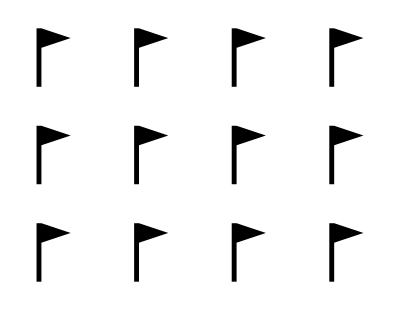
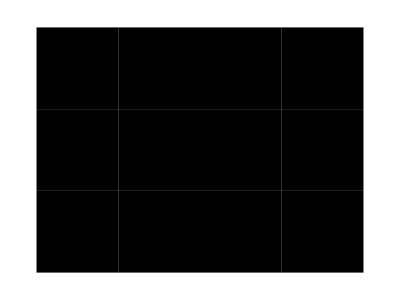
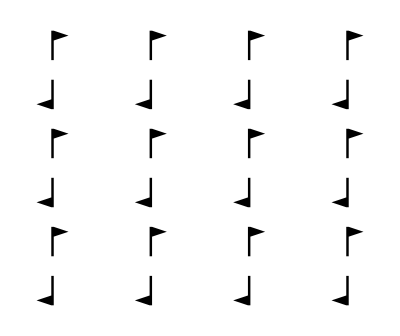
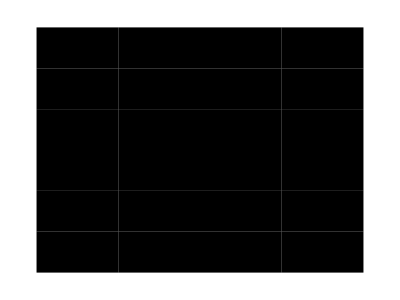
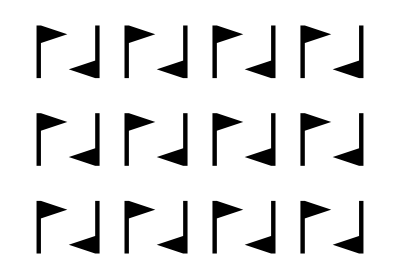
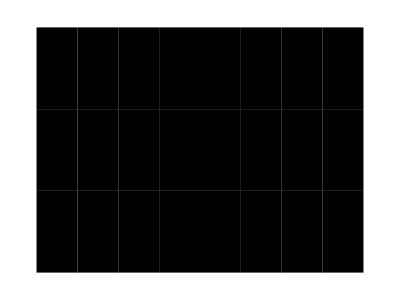
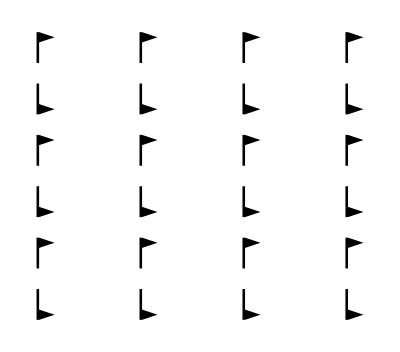
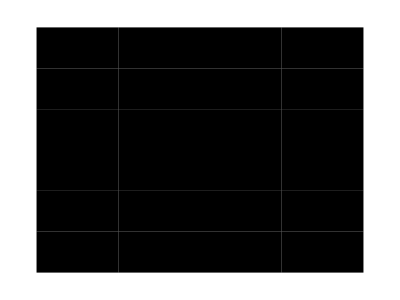
{{p1,-Graphics-,-Graphics-},{p2 h,-Graphics-,-Graphics-},{p2 v,-Graphics-,-Graphics-},{p11m,-Graphics-,-Graphics-},{p1m1,-Graphics-,-Graphics-},{p11g,-Graphics-,-Graphics-},{p1g1,-Graphics-,-Graphics-},{c11m,-Graphics-,-Graphics-},{c1m1,-Graphics-,-Graphics-},{p2mm,-Graphics-,-Graphics-},{p2mg,-Graphics-,-Graphics-},{p2gm,-Graphics-,-Graphics-},{p2gg h,-Graphics-,-Graphics-},{p2gg v,-Graphics-,-Graphics-},{c2mm h,-Graphics-,-Graphics-},{c2mm v,-Graphics-,-Graphics-},{p4 a,-Graphics-,-Graphics-},{p4 d,-Graphics-,-Graphics-},{p4m,-Graphics-,-Graphics-},{p4g,-Graphics-,-Graphics-},{p3 p,-Graphics-,-Graphics-},{p3 e,-Graphics-,-Graphics-},{p31m,-Graphics-,-Graphics-},{p3m1,-Graphics-,-Graphics-},{p6 p,-Graphics-,-Graphics-},{p6 e,-Graphics-,-Graphics-},{p6m,-Graphics-,-Graphics-}}

```mathematica
DisplayAll[{2,2},4,3,{Blue,Green,Yellow,Red},{Blue,Green,Red}]
```

## Old: Sampled Image

Makes an image from another image by tiling the original image using various symmetries.

TileImage[center_,tlfunc_,tlfparams_,nsamps_,img_]
Args:
Center for the transformation (horizontal, vertical)
Transformation function on pixel coordinates
Args parameters coords - returns new coords
Parameters for that function
Number of samples per pixel (at least 1: more is smoother but more time-consuming))
Mma image object

Returns transformed image

Rosette[center_,params_,nsamps_,img_]
Args:
Center
Params: list of
- Starting angle in radians
 - Number of divisions
 - Whether cyclic (False) or dihedral (True)
Number of samples per pixel
Mma image object

Returns transformed image

Types: C(n), D(n)

Frieze[center_,params_,nsamps_,img_] 
Args:
Center
Params:
- Type: 1 to 7
- Starting angle in radians
- Length of repeat
- Starting angle of second line in radians (only for 1, 5)
Number of samples per pixel
Mma image object

Returns transformed image

Types: p1, p11m, p11g, p1m1 p2, p2mm, p2mg

Wallpaper[center_,params_,nsamps_,img_]
Args:
Center
Params:
- Type: 1 to 17
- Starting angle in radians
- Length of repeat
- Starting angle of second line in radians (1, 2, 5, 9)
- Length of second repeat (1 to 4, 6 to 8)
Number of samples per pixel
Mma image object

Returns transformed image

Types: p1, p2, pm, pg, cm, pmm, pmg, pgg, cmm, p4, p4m, p4g, p3, p3m1, p31m, p6, p6m

LogSpiral[center_,params_,nsamps_,img_] 
Args:
Center
Params
- Starting angle in radians
- Starting radius
- Pitch
Number of samples per pixel
Mma image object

Returns transformed image

```mathematica
(* Creates an array of indices and works with it *)
```

```mathematica
TileImage[center_,tlfunc_,tlfparams_,nsamps_,img_] := Module[{srcimg,srcdata,dstdata,nh,nv,nhxt,nvxt,ixs,tfct,clpf,prfc},
(* Need to reflect the image to count the center from the bottom instead of from the top *)
srcimg = ImageReflect[Image[img,"Real"]];
srcdata = ImageData[srcimg];
(* Horizontal, then vertical *)
{nh,nv} = ImageDimensions[srcimg];

(* For each destination pixel, its source-pixel index. Indexed vertical, horizontal. Made oversized to do antialiasing *)
nhxt = nsamps*nh; nvxt = nsamps*nv;
ixs = (Outer[List,Range[nvxt],Range[nhxt]] - 0.5)/nsamps + 0.5;
ixs = Map[Reverse[#]-center&,ixs,{2}];
ixs = Map[tlfunc[tlfparams,#]&,ixs,{2}];
ixs = Map[Reverse[#]+center&,ixs,{2}];
ixs = Round[ixs];
ixs = Map[{Clip[#[[1]],{1,nv}],Clip[#[[2]],{1,nh}]}&,ixs,{2}];
(* Get the new image *)
dstdata = Map[srcdata[[#[[1]],#[[2]]]]&,ixs,{2}];

(* Undo that reflection, get to the original size *)
ImageReflect[ImageResize[Image[dstdata],{nh,nv}]]
]
```

```mathematica
(* The original version: point by point *)
```

```mathematica
OldTileImage[center_,tlfunc_,tlfparams_,nsamps_,img_] := Module[{srcimg,srcdata,dstdata,zero,nsr,cv,ch,nv,nh,iv,ih,jv,jh,kv,kh,lv,lh,prs},
{ch,cv} = center;
(* Need to reflect the image to count the center from the bottom instead of from the top *)
srcimg = ImageReflect[Image[img,"Real"]];
srcdata = ImageData[srcimg];
{nh,nv} = ImageDimensions[srcimg];
nsr = 1.0/nsamps;
dstdata = nsr^2*Table[Sum[
kv = iv + (1/2)*(nsr*(2*jv-1)-1) - cv; 
kh = ih + (1/2)*(nsr*(2*jh-1)-1) - ch;
prs =  tlfunc[tlfparams,{kh,kv}];
lv = Round[prs[[2]] + cv]; 
lv = Min[Max[lv,1],nv];
lh = Round[prs[[1]] + ch];
lh = Min[Max[lh,1],nh];
srcdata[[lv,lh]],
{jv,nsamps},{jh,nsamps}],{iv,nv},{ih,nh}];
(* Undo that reflection *)
ImageReflect[Image[dstdata]]
]
```

```mathematica
(* For rosette groups *)
```

```mathematica
RosetteTlf[params_,pt_] := Module[{a0,n,cd,x,y,r,a},
{a0,n,cd} = params;
{x,y} = pt;
r = Sqrt[x^2+y^2];
a = If[x == 0 && y == 0,0, ArcTan[x,y]];
a = Mod[(n/(2*Pi))*(a-a0),1];
If[cd,If[a > 1/2,a = 1 - a]];
a = a0 + ((2*Pi)/n)*a;
r*{Cos[a],Sin[a]}
]
```

```mathematica
Rosette[center_,params_,nsamps_,img_] := 
TileImage[center,RosetteTlf,params,nsamps,img]
```

```mathematica
(* For lattice groups *)
```

```mathematica
LatticeTlf[params_,pt_] := Module[{lat,invlat,tlfunc,tlfparams,ptx},
{lat,invlat,tlfunc,tlfparams} = params;
ptx = invlat.pt;
ptx = tlfunc[tlfparams,ptx];
lat.ptx]
```

```mathematica
LatticeTileImage[center_,latparams_,tlfunc_,tlfparams_,nsamps_,img_] := Module[{a1,l1,a2,l2,lat,invlat,ltfparams},
{a1,l1,a2,l2} = latparams;
lat =1.0*{{l1*Cos[a1],l2*Cos[a2]},{l1*Sin[a1],l2*Sin[a2]}};
invlat = Inverse[lat];
ltfparams = {lat,invlat,tlfunc,tlfparams};
TileImage[center,LatticeTlf,ltfparams,nsamps,img]
]
```

```mathematica
(* For frieze groups *)
```

```mathematica
FriezeTlf[params_,pt_] := Module[{type,x,y},
{x,y} = pt;
type = params;
x = Mod[x,1];
Switch[type,
1,
Null,
2,
If[y < 0, y *= -1],
3,
If[x > 1/2, y *= -1],
4,
If[x > 1/2,x *= -1],
5,
If[y < 0, x *= -1; y*= -1],
6,
If[y < 0, y *= -1]; If[x > 1/2, x *= -1],
7,
If[y < 0,  x += 1/2;x = Mod[x,1]; y *= -1]; If[x > 1/2, x *= -1]
];
x = Mod[x,1];
{x,y}]
```

```mathematica
Frieze[center_,params_,nsamps_,img_] := Module[{type,a1,l1,a2,l2},
type = First[params];
Which[MemberQ[{1,5},type],{type,a1,l1,a2} = params,
MemberQ[{2,3,4,6,7},type],{type,a1,l1} = params;a2 = a1 + Pi/2,
True,Return[]];
l2 = l1;
LatticeTileImage[center,{a1,l1,a2,l2},FriezeTlf,type,nsamps,img]
]
```

```mathematica
(* For wallpaper groups *)
```

```mathematica
WallpaperTlf[params_,pt_] := Module[{type,x,y,z},
{x,y} = pt;
type = params;
x = Mod[x,1]; y = Mod[y,1];
Switch[type,
1,
Null,
2,
If[y > 1/2, x *= -1; y *= -1],
3,
If[y > 1/2, y *= -1],
4,
If[y > 1/2, x += 1/2;x = Mod[x,1];y *= -1],
5,
If[y > x, z = x; x = y; y = z],
6,
If[x > 1/2, x *= -1]; If[y > 1/2, y *= -1],
7,
If[y > 1/2,x += 1/2; x = Mod[x,1]; y *= -1]; If[x > 1/2, x *= -1],
8,
If[y > 1/2, x *= -1; y *= -1;x = Mod[x,1]; y = Mod[y,1]];If[x+y < 1/2,x+= 1/2; y = 1/2 - y]; If[x-y > 1/2, x -= 1/2; y = 1/2 - y],
9,
If[x+y ≥1, z = x; x = y; y = z; x *= -1; y *= -1]; If[y > x, z = x; x = y; y = z],
10,
If[y > 1/2, If[x > 1/2,x = 1-x; y = 1-y, z = x; x = y; y = z; x *= -1], If[x > 1/2, z = x; x = y; y = z; y *= -1]],
11,
If[y > 1/2, If[x > 1/2,x = 1-x; y = 1-y, z = x; x = y; y = z; x *= -1], If[x > 1/2, z = x; x = y; y = z; y *= -1]]; x = Mod[x,1]; y = Mod[y,1]; If[y > x, z = x; x = y; y = z],
12,
If[y > 1/2, If[x > 1/2,x = 1-x; y = 1-y, z = x; x = y; y = z; x *= -1], If[x > 1/2, z = x; x = y; y = z; y *= -1]]; x = Mod[x,1]; y = Mod[y,1]; If[x+y > 1/2, z = x; x = y; y = z; x = 1/2-x; y = 1/2-y],
13,
If[y > x,If[2x+y < 1,z = y; y = -x-y + 1; x = z]; If[x+2y > 2,z = x; x = -x-y + 2; y = z], If[x+2y < 1, z = x; x = -x-y + 1; y = z];If[2x+y > 2,z = y; y = -x-y + 2; x = z]],
14,
If[y > x,If[2x+y < 1,z = y; y = -x-y + 1; x = z]; If[x+2y > 2,z = x; x = -x-y + 2; y = z], If[x+2y < 1, z = x; x = -x-y + 1; y = z];If[2x+y > 2,z = y; y = -x-y + 2; x = z]];
If[y > x,z = x; x = y; y = z],
15,
If[y > x,If[2x+y < 1,z = y; y = -x-y + 1; x = z]; If[x+2y > 2,z = x; x = -x-y + 2; y = z], If[x+2y < 1, z = x; x = -x-y + 1; y = z];If[2x+y > 2,z = y; y = -x-y + 2; x = z]];
If[x+y>1,z = x; x = y; y = z; x*= -1; y *= -1],
16,
If[y > x,If[2x+y < 1,z = y; y = -x-y + 1; x = z]; If[x+2y > 2,z = x; x = -x-y + 2; y = z], If[x+2y < 1, z = x; x = -x-y + 1; y = z];If[2x+y > 2,z = y; y = -x-y + 2; x = z]];
If[x+y>1, x*= -1; y *= -1],
17,
If[y > x,If[2x+y < 1,z = y; y = -x-y + 1; x = z]; If[x+2y > 2,z = x; x = -x-y + 2; y = z], If[x+2y < 1, z = x; x = -x-y + 1; y = z];If[2x+y > 2,z = y; y = -x-y + 2; x = z]];
If[x+y>1,z = x; x = y; y = z; x*= -1; y *= -1];x = Mod[x,1]; y = Mod[y,1];If[y > x, z = x; x = y; y = z]
];
x = Mod[x,1]; y = Mod[y,1];
{x,y}]
```

```mathematica
Wallpaper[center_,params_,nsamps_,img_] :=  Module[{type,a1,l1,a2,l2},
type = First[params];
Which[MemberQ[{1,2},type],{type,a1,l1,a2,l2} = params,
MemberQ[{3,4,6,7,8},type],{type,a1,l1,l2} = params;a2 = a1 + Pi/2,
MemberQ[{5,9},type], {type,a1,l1,a2} = params;l2 = l1,
MemberQ[{10,11,12},type],{type,a1,l1} = params;a2 = a1 + Pi/2; l2 = l1,
MemberQ[{13,14,15,16,17},type],{type,a1,l1} = params;a2 = a1 + Pi/3; l2 = l1,
True,Return[]];
LatticeTileImage[center,{a1,l1,a2,l2},WallpaperTlf,type,nsamps,img]
]
```

```mathematica
(* For the logarithmic spiral -- just do p1 for now. Can use other wallpaper groups if desired. *)
```

```mathematica
LogSpiralTlf[params_,pt_] := Module[{a0,r0,pitch,rptang,x,y,r,a,lra,n,rx},
{a0,r0,pitch,rptang} = params;
x  = pt[[1]]; y = pt[[2]];
r = Sqrt[x^2+y^2]; a = If[x==0&&y==0,0,ArcTan[x,y]] - a0;
If[r==0,Return[r0*{Cos[a0],Sin[a0]}]];
lra = Log[r/r0]/pitch  - a;
n = Floor[lra/(2*Pi)];
lra -= (2*Pi)*n;
a += (2*Pi)*n;
a -= rptang*Floor[a/rptang];
rx = r0*Exp[pitch*(lra+a)];
a += a0;
rx*{Cos[a],Sin[a]}
]
```

```mathematica
LogSpiral[center_,params_,nsamps_,img_] := 
TileImage[center,LogSpiralTlf,params,nsamps,img]
```

```mathematica
(* Test images *)
```

```mathematica
rose = Import["ExampleData/rose.gif"];
```

```mathematica
Dimensions[ImageData[rose]]
```

{164,223,3}

```mathematica
lena = Import["ExampleData/lena.tif"]
```

-Graphics-

```mathematica
Dimensions[ImageData[lena]]
```

{116,150,3}

```mathematica
(* Tests *)
```

```mathematica
Table[Rosette[{75,58},{0,k,rfl},1,lena] ,{k,1,5},{rfl,{False, True}}]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
Table[Frieze[{75,58},{t,0,50,Pi/3},1,lena],{t,{1,5}}]
```

{-Graphics-,-Graphics-}

```mathematica
Table[Frieze[{75,58},{t,0,50},1,lena],{t,{2,3,4,6,7}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Wallpaper[{75,58},{t,0,80,5Pi/12,50},1,lena],{t,{1,2}}]
```

{-Graphics-,-Graphics-}

```mathematica
Wallpaper[{75,58},{#,0,80,50},1,lena]& /@ {3,4,6,7,8}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Wallpaper[{75,58},{#,0,50,5Pi/12},1,lena]& /@ {5,9}
```

{-Graphics-,-Graphics-}

```mathematica
Wallpaper[{75,58},{#,0,50},1,lena]& /@ {10,11,12}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Wallpaper[{75,58},{#,0,50},1,lena]& /@ {13,14,15,16,17}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
LogSpiral[{75,58},{0,25,0.1,(3/7)*Pi},1,lena]
```

-Graphics-

```mathematica
(* Rotation from combination of skews -- fast alternative *)
```

```mathematica
skewx[t_] := {{1,t},{0,1}}
```

```mathematica
skewy[t_] := {{1,0},{t,1}}
```

```mathematica
(* t = tan((1/2)*(rotation angle)) *)
```

```mathematica
{(skewx[-t].skewy[2t/(1+t^2)].skewx[-t] - {{cs,-sn},{sn,cs}}),(cs^2+sn^2)-1} /. {cs->(1-t^2)/(1+t^2),sn->(2t)/(1+t^2)}// Factor
```

{{{0,0},{0,0}},0}

## Plane tilings for all curvatures

Here, all curvatures are constant, giving full symmetry of the space.
- Positive: sphere -- tilings are polyhedra
- Zero: plane
- Negative: hyperbolic plane

These tilings are tilings of
Schwarz triangle - Wikipedia
https://en.wikipedia.org/wiki/Schwarz_triangle

Triangles with angles pi/n1, pi/n2, pi/n3
The sum 1/n1 + 1/n2 + 1/n3 is related to the space curvature:
Positive: >1
Zero: =1
Negative: <1

There are a finite number of solutions for positive and zero curvature.
Positive: 2,2,n . 2,3,3 . 2.3.4 . 2.3.5
Zero: 2,3,6 . 2,4,4 . 3.3.3
Negative: all the rest

Algorithm:
Generate initial triangle
Generate next triangles by flipping each triangle over each edge

I have not been able to discover any broader algorithm, like there is for positive and zero curvature.

MakeTriangles[ns_,ntri_]
ns -- parameters: {n1,n2,n3}
ntri -- number of triangles to make, stops if closed
Returns {curvature, vertices, triangles}
Triangle: {vertices, parity (1,-1)}

The surface is embedded in a space: x, y, z
Surface constraints:
Sphere: x^2 + y^2 + z^2 = 1
Plane: z = const.
Hyperbolic plane: - x^2 - y^2 + z^2 = 1

DisplayTriangles[trix_,proj_,tclr_]
trix - output of MakeTriangles
proj: for non-flat output,
“3D” - Mathematica’s 3D viewer (movable orthographic)
“Gnomonic” - Straight-Line Geodesic: {x,y}/z
“Conformal” - Stereographic, Equal-Angle: {x,y}/(1+z)
“Equal-Area”: {x,y}/sqrt(2*(1+z))
tclr - color function:
- Arg - the “Triangle” object above
- Returns - color, Line, Polygon objects for Graphics, Graphics3D

Geodesics:
Sphere: X = P*cos(t) + Q*sin(t), X.X = P.P = Q.Q = 1, P.Q = 0
Plane: straight line: X = X0 + X1*t
Hyp Pln: X = P*cosh(t) + Q*sinh(t), X.X = P.P = 1, Q.Q = -1, P.Q = 0
Tangent: T = dX/dt
Angle: cos(a) = (T1.T2)/sqrt((T1.T1)*(T2.T2))

Links:
Uniform tilings in hyperbolic plane - Wikipedia - https://en.wikipedia.org/wiki/Uniform_tilings_in_hyperbolic_plane
Hyperbolic Planar Tesselations - http://www.plunk.org/~hatch/HyperbolicTesselations/
Don Hatch’s Home Page - http://www.plunk.org/~hatch/ -- has some source code
Hyperbolic Tessellations - http://aleph0.clarku.edu/~djoyce/poincare/poincare.html
Hyperbolic Tilings - Math Images - http://mathforum.org/mathimages/index.php/Hyperbolic_Tilings
Wolfram Demonstrations Project - http://demonstrations.wolfram.com/TilingTheHyperbolicPlaneWithRegularPolygons/ -- this and related ones may have useful Mma source code
The Geometry Page - http://superliminal.com/geometry/geometry.htm
Virtual Reality Polyhedra - http://www.georgehart.com/virtual-polyhedra/vp.html
Symmetry, Crystals and Polyhedra - http://www.uwgb.edu/dutchs/symmetry/symmetry.htm
The Geometry Junkyard: Hyperbolic Tiling - https://www.ics.uci.edu/~eppstein/junkyard/hypertile.html

## Display of Tilings

### Functions

```mathematica
ThirdVertex[dgmet_,vt1_,vt2_,ca1_,ca2_,s_] := Module[{mv1,mv2,mdet,pv11,pv12,pv22,pvdet},
mv1 = dgmet*vt1; mv2 = dgmet*vt2;
mdet = Times @@ dgmet;
pv11 = mv1.vt1; pv12 = mv1.vt2; pv22 = mv2.vt2;
pvdet = pv11*pv22 - pv12^2;
(vt1*(pv22*ca1-pv12*ca2) + vt2*(pv11*ca2 - pv12*ca1) + Cross[mv1,mv2]*s*Sqrt[(pvdet - (pv22*ca1^2-2pv12*ca1*ca2+pv11*ca2^2))/mdet])/pvdet
]
```

```mathematica
ThirdVertexVerify[dgmet_,vt1_,vt2_,ca1_,ca2_,s_] := Module[{vt3},
vt3 = ThirdVertex[dgmet,vt1,vt2,ca1,ca2,s];
{(dgmet*vt1).vt3 - ca1,(dgmet*vt2).vt3 - ca2, (dgmet*vt3).vt3 - 1} // Factor
]
```

```mathematica
Table[ThirdVertexVerify[Array[g,3],Array[n1,3],Array[n2,3],c1,c2,s],{s,-1,1,2}]
```

{{0,0,0},{0,0,0}}

```mathematica
VertexReflection[dgmet_,vt1_,vt2_,vt3_] := Module[{mv1,mv2,pv11,pv12,pv22,ca1,ca2},
mv1 = dgmet*vt1; mv2 = dgmet*vt2;
pv11 = mv1.vt1; pv12 = mv1.vt2; pv22 = mv2.vt2;
ca1 = mv1.vt3; ca2 = mv2.vt3;
2(vt1*(pv22*ca1-pv12*ca2) + vt2*(pv11*ca2 - pv12*ca1))/(pv11*pv22 - pv12^2) - vt3
]
```

```mathematica
Table[VertexReflection[Array[g,3],Array[n1,3],Array[n2,3],ThirdVertex[Array[g,3],Array[n1,3],Array[n2,3],c1,c2,s]] - ThirdVertex[Array[g,3],Array[n1,3],Array[n2,3],c1,c2,-s],{s,-1,1,2}] // Factor
```

{{0,0,0},{0,0,0}}

```mathematica
PlaneVertexReflection[vt1_,vt2_,vt3_] := Module[{vt12,vt13},
vt12 = vt2 - vt1;
vt13 = vt3 - vt1;
vt1 + (2((vt12.vt13)/(vt12.vt12))*vt12 - vt13)
]
```

```mathematica
GeneralVertexReflection[curv_,vt1_,vt2_,vt3_] := Which[curv>0,VertexReflection[{1,1,1},vt1,vt2,vt3],curv==0,PlaneVertexReflection[vt1,vt2,vt3],curv<0,VertexReflection[{-1,-1,1},vt1,vt2,vt3]]
```

```mathematica
MakeInitialTriangle[ns_] := Module[{curv,angs,c12,c13,s12,s13,v1,v2,v3},
(* Curvature value *)
curv = Sign[Total[1/ns[[;;3]]]-1];
(* Initial triangle *)
angs = Pi/ns[[;;3]] // N;
c12 = (Cos[angs[[3]]] + Cos[angs[[1]]]*Cos[angs[[2]]])/(Sin[angs[[1]]]*Sin[angs[[2]]]);
c13 = (Cos[angs[[2]]] + Cos[angs[[1]]]*Cos[angs[[3]]])/(Sin[angs[[1]]]*Sin[angs[[3]]]);
Which[curv>0,
(* Sphere - use spherical trigonometry *)
s12 = Sqrt[1-c12^2];
s13 = Sqrt[1-c13^2];
v1 = {0,0,1};
v2 = {s12,0,c12};
v3 = {s13*Cos[angs[[1]]],s13*Sin[angs[[1]]],c13},
curv == 0,
(* Plane - use law of sines *)
s12 = Sin[angs[[3]]];
s13 = Sin[angs[[2]]];
v1 = {0,0};
v2 = {s12,0};
v3 = {s13*Cos[angs[[1]]],s13*Sin[angs[[1]]]},
curv < 0,
(* Hyperbolic plane - analytically continue the spherical trig *)
s12 = Sqrt[c12^2-1];
s13 = Sqrt[c13^2-1];
v1 = {0,0,1};
v2 = {s12,0,c12};
v3 = {s13*Cos[angs[[1]]],s13*Sin[angs[[1]]],c13}
];
(* Emit the curvature also *)
{curv,{v1,v2,v3}}
]
```

```mathematica
VtxDistance[curv_,vtx_] := Which[curv>0,-vtx[[3]],curv==0,vtx.vtx,curv<0,vtx[[3]]]
```

```mathematica
MakeTriTolerance = 10.^(-8);
```

```mathematica
MakeTriangles[ns_,ntri_] := Module[{curv,vts,vtdists,tris,vttrixs,eds,kx,edvts,vtix1,edsvt1,evoth,vtix2,triix,tri,vtix3,vtrfl,ixrfl,ix,ntvts,ntrvts,ntreds},
(* The first triangle. Setup includes a function for getting triangle memberships for each vertex. That successfully optimizes the code; allocating arrays in advance for the vertices and triangles doesn't. *)
{curv,vts} = MakeInitialTriangle[ns];
vtdists = VtxDistance[curv,#]& /@ vts;
Do[vttrixs[k] = {1},{k,3}];
tris = {{{1,2,3},1}};
(* Boundary edges. Use this to reduce calculation load *)
eds = {{1,2},{1,3},{2,3}};
Do[(* Is the surface closed? *)
If[ Length[eds] <= 0,Break[]];
(* Find the closest vertex *)
edvts = Union[Flatten[eds]];
vtix1 = edvts[[First[Ordering[vtdists[[edvts]],1]]]];
(* Find the second-closest vertex that's in an edge *)
edsvt1 = Select[eds,MemberQ[#,vtix1]&];
evoth = First[Complement[#,{vtix1}]]& /@ edsvt1;
vtix2 = evoth[[First[Ordering[vtdists[[evoth]],1]]]];
(* Find the triangle that contains both of them *)
triix = First[Intersection[vttrixs[vtix1],vttrixs[vtix2]]];
tri = tris[[triix]];
vtix3 = First[Complement[tri[[1]],{vtix1,vtix2}]];
(* Construct the reflected triangle. *)
vtrfl = GeneralVertexReflection[curv,vts[[vtix1]],vts[[vtix2]],vts[[vtix3]]];
ixrfl = Length[vts] + 1;
(* Is the new vertex an existing one? *)
Do[If[((#.#)& @ (vtrfl-vts[[ix]])) < MakeTriTolerance^2,
ixrfl = ix; Break[]],{ix,edvts}];
(* Compose the new triangle *)
AppendTo[vttrixs[vtix1],Length[tris]+1];
AppendTo[vttrixs[vtix2],Length[tris]+1];
If[ixrfl > Length[vts],
AppendTo[vts,vtrfl];
AppendTo[vtdists, VtxDistance[curv,vtrfl]];
vttrixs[Length[vts]] = {Length[tris]+1},
AppendTo[vttrixs[ixrfl],Length[tris]+1]
];
ntrvts = Table[If[tri[[1,k]] == vtix3,ixrfl,tri[[1,k]]],{k,3}];
AppendTo[tris,{ntrvts,-tri[[2]]}];
ntreds =Sort[ntrvts[[#]]]& /@ {{1,2},{1,3},{2,3}};
eds = Union[Complement[eds,ntreds],Complement[ntreds,eds]],
{kx,ntri-1}];
{curv,vts,tris}
]
```

```mathematica
TrimVertices[vts_,tris_,cond_] := Module[{vtconds,vtixs,selixs,ngslixs,trimvts,trimtris,k,tmixs},
vtconds = cond /@ vts;
vtixs = Range[Length[vts]];
selixs = #[[2]]& /@ Select[Transpose[{vtconds,vtixs}],#[[1]]&];
ngslixs = Complement[vtixs,selixs];
trimvts = vts[[selixs]];
trimtris = Select[tris,Length[Complement[#[[1]],ngslixs]] == 3&];
Do[tmixs[selixs[[k]]] = k,{k,Length[selixs]}];
trimtris = {tmixs /@ #[[1]],#[[2]]}& /@ trimtris;
{trimvts,trimtris}
]
```

```mathematica
DisplayTriangles[trix_,proj_,tclr_] := Module[{curv,vts,tris,vtsx,trisx},
{curv,vts,tris} = trix;
If[curv ≠ 0,
Switch[proj,
"3D",
Graphics3D[GraphicsComplex[vts,tclr /@ tris],SphericalRegion->True],
"Gnomonic",
{vtsx,trisx} = TrimVertices[vts,tris,#[[3]]>MakeTriTolerance&];
vtsx = {#[[1]],#[[2]]}/#[[3]]& /@ vtsx;
Graphics[GraphicsComplex[vtsx,tclr /@ trisx]],
"Conformal",
{vtsx,trisx} = TrimVertices[vts,tris,#[[3]]>-1+MakeTriTolerance&];
vtsx = {#[[1]],#[[2]]}/(1+#[[3]])& /@ vtsx;
Graphics[GraphicsComplex[vtsx,tclr /@ trisx]],
"Equal-Area",
{vtsx,trisx} = TrimVertices[vts,tris,#[[3]]>-1+MakeTriTolerance&];
vtsx = {#[[1]],#[[2]]}/Sqrt[2(1+#[[3]])]& /@ vtsx;
Graphics[GraphicsComplex[vtsx,tclr /@ trisx]]
],
Graphics[GraphicsComplex[vts,tclr /@ tris]]
]
]
```

```mathematica
TriColorBoth = {Red, Green, Blue};
```

```mathematica
TriColorPos = Lighter /@ TriColorBoth;
```

```mathematica
TriColorNeg = Darker /@ TriColorBoth;
```

```mathematica
TriColored[tri_] := {EdgeForm[],Polygon[tri[[1]],VertexColors->TriColorBoth]}
```

```mathematica
ParTriColored[tri_] := {EdgeForm[],Polygon[tri[[1]],VertexColors->If[tri[[2]]≥0,TriColorPos,TriColorNeg]]}
```

```mathematica
Bdries[tri_,i1_,i2_] := {Black,Line[{tri[[1,i1]],tri[[1,i2]]}],EdgeForm[{}],LightGray,Polygon[tri[[1]]]}
```

```mathematica
Bdries12[tri_] := Bdries[tri,1,2]
```

```mathematica
Bdries13[tri_] := Bdries[tri,1,3]
```

```mathematica
Bdries23[tri_] := Bdries[tri,2,3]
```

### Displays

To use, enter the angle numbers in the first three input fields and the number of triangles to make in the fourth.

The triangles have angles pi/(angle-number).

```mathematica
NumCheck[x_,minval_] := If[IntegerQ[#],#,minval]& @ Max[Round[x],minval]
```

Initial values: the three angle numbers and the number of triangles

```mathematica
NumAng1 = 2; NumAng2 = 3; NumAng3 = 7; NumTris = 1000;
```

Input the three angle numbers

```mathematica
{InputField[Dynamic[NumAng1],Number],Dynamic[NumCheck[NumAng1,2]]}
```

{,}

```mathematica
{InputField[Dynamic[NumAng2],Number],Dynamic[NumCheck[NumAng2,2]]}
```

{,}

```mathematica
{InputField[Dynamic[NumAng3],Number],Dynamic[NumCheck[NumAng3,2]]}
```

{,}

Input the number of triangles to make

```mathematica
{InputField[Dynamic[NumTris],Number],Dynamic[NumCheck[NumTris,1]]}
```

{,}

```mathematica
(* Need to get initial values in place *)
```

```mathematica
{TriTime,Tris} = Timing[MakeTriangles[{NumAng1,NumAng2,NumAng3},NumTris]];
```

```mathematica
Button["Make the triangles",{TriTime,Tris} = Timing[MakeTriangles[{NumAng1,NumAng2,NumAng3},NumTris]]]
```

Make the triangles

```mathematica
Dynamic[{TriTime,Length /@ Tris}]
```

```mathematica
Manipulate[DisplayTriangles[Tris,proj,tclr],{{proj,"Conformal"},{"3D","Gnomonic","Conformal","Equal-Area"}},{{tclr,ParTriColored},{TriColored,ParTriColored,Bdries12,Bdries13,Bdries23}}]
```

## Projections of Shapes

### Projections

EA: Equal area
Ortho: orthographic, like viewing from a distance
Stereo: stereographic: conformal (equal angles, shapes)
Gnom: gnomonic: geodesic -> geodesic
A geodesic generalizes the straight line in flat space; it’s the shortest distance between two points.

These projections work for all the spaces here, and for flat space, add 1 to the two components.

```mathematica
ProjDenom["EA",z_]  := Sqrt[2(1+z)]
```

```mathematica
ProjDenom["Ortho",z_] := 1
```

```mathematica
ProjDenom["Stereo",z_] := 1+z
```

```mathematica
ProjDenom["Gnom",z_] := z
```

```mathematica
Proj[type_,vec_List] := Most[vec]/ProjDenom[type,Last[vec]]
```

### Inner Product and Magnitude

The inner product is good for finding angles between two geodesics, and the magnitude is for spherical and hyperbolic spaces; it ought to be 1.

```mathematica
InnProdSph[x_List,y_List] := x.y
```

```mathematica
MagSph[x_List] := InnProdSph[x,x]
```

```mathematica
InnProdFlat[x_List,y_List] := x.y
```

```mathematica
MagFlat[x_List] := InnProdFlat[x,x]
```

```mathematica
InnProdHyp[x_List,y_List] := Last[x]*Last[y] - InnProdSph[Most[x],Most[y]]
```

```mathematica
MagHyp[x_List] := InnProdHyp[x,x]
```

### Line

Or more generally, geodesic.
Offset from center (impact parameter): b
Distance along line: s

```mathematica
GeodSph = {Sin[b]*Cos[s],Sin[s],Cos[b]*Cos[s]}; MagSph[GeodSph] // TrigReduce
```

1

```mathematica
MagSph[D[GeodSph,s]] // TrigReduce
```

1

```mathematica
Proj["Gnom",GeodSph]
```

{Tan[b],Sec[b] Tan[s]}

```mathematica
(* Obviously a line *)
```

```mathematica
GeodHyp = {Sinh[b]*Cosh[s],Sinh[s],Cosh[b]*Cosh[s]}; MagFlat[Proj["Stereo",GeodSph] - {-Cot[b],0}] - (Csc[b])^2 // TrigToExp // Factor
```

0

```mathematica
(* An offset circle *)
```

```mathematica
MagHyp[GeodHyp] // TrigReduce
```

1

```mathematica
MagHyp[D[GeodHyp,s]] // TrigReduce
```

-1

```mathematica
Proj["Gnom",GeodHyp]
```

{Tanh[b],Sech[b] Tanh[s]}

```mathematica
(* Also obviously a line *)
```

```mathematica
MagFlat[Proj["Stereo",GeodHyp] - {Coth[b],0}] - (Csch[b])^2 //TrigToExp // Factor
```

0

```mathematica
(* Also an offset circle *)
```

### Circle

Radius of circle: r
Angle from positive first coordinate: a
Tilt angle: t

```mathematica
CircSph = {Sin[r]*Cos[a],Sin[r]*Sin[a],Cos[r]}; MagSph[CircSph] // TrigReduce
```

1

```mathematica
CircTiltSph = {{Cos[t],0,-Sin[t]},{0,1,0},{Sin[t],0,Cos[t]}}.CircSph; MagSph[CircTiltSph] // TrigReduce
```

1

```mathematica
MagFlat[Proj["Stereo",CircTiltSph] - {-Sin[t]/(Cos[r]+Cos[t]),0}] - (Sin[r]/(Cos[r]+Cos[t]))^2 // TrigToExp // Factor
```

0

```mathematica
CircHyp = {Sinh[r]*Cos[a],Sinh[r]*Sin[a],Cosh[r]}; MagHyp[CircHyp] // TrigReduce
```

1

```mathematica
CircTiltHyp= {{Cosh[t],0,-Sinh[t]},{0,1,0},{-Sinh[t],0,Cosh[t]}}.CircHyp; MagHyp[CircTiltHyp] // TrigReduce
```

1

```mathematica
MagFlat[Proj["Stereo",CircTiltHyp] - {-Sinh[t]/(Cosh[r]+Cosh[t]),0}] - (Sinh[r]/(Cosh[r]+Cosh[t]))^2 // TrigToExp // Factor
```

0

```mathematica
CoefficientList[Series[CircTiltHyp /. {t->r+e*b,a->e*a},{e,0,2}],e] /. Cosh[r]^2->1+Sinh[r]^2 // Factor
```

{{0,-b,-1/2 a^2 Cosh[r] Sinh[r]},{0,a Sinh[r]},{1,0,1/2 (b^2+a^2 Sinh[r]^2)}}

```mathematica
Expand[Expand[TrigExpand[Normal[Series[CircTiltHyp,{a,0,2}]] /. t->r+b] /. a->ax*Sech[r]] /. Sech[r]^2->1-Tanh[r]^2] /. Tanh[r]->1
```

{-1/2 ax^2 Cosh[b]-Sinh[b]-1/2 ax^2 Sinh[b],ax,Cosh[b]+1/2 ax^2 Cosh[b]+1/2 ax^2 Sinh[b]}

```mathematica
InfCirc = {-Sinh[b] - ax^2*Exp[b]/2,ax,Cosh[b] + ax^2*Exp[b]/2}; MagHyp[InfCirc] // TrigToExp // Expand
```

1

```mathematica
MagFlat[Proj["Stereo",InfCirc] -{-Exp[b]/(Exp[b]+1),0}]- 1/(Exp[b]+1)^2 //TrigToExp // Factor
```

0